See baseflow.tex write up for the background on this notebook.

```mathematica
<<"Utilities`CleanSlate`";
CleanSlate[];
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 37 Kb

```mathematica
Needs["VectorAnalysis`"];
SetCoordinates[Cylindrical];
With[{f=phi[Rr]},With[{gf=Simplify[Grad[f]],lf=Simplify[Laplacian[f]]},With[{gf2=Simplify[DotProduct[gf,gf]]},lf-(Ma^2/2) DotProduct[gf,Grad[gf2]]-(gamma0-1)(Ma^2/2)(gf2-1)lf]]];
Collect[%,{phi''[Rr],phi'[Rr],phi[Rr]}];
Map[Simplify,%];
resphi=%
```

((2+(-1+gamma0) Ma^2) phi'[Rr])/(2 Rr)-((-1+gamma0) Ma^2 phi'[Rr]^3)/(2 Rr)-1/2 (-2-(-1+gamma0) Ma^2+(1+gamma0) Ma^2 phi'[Rr]^2) phi''[Rr]

```mathematica
r resphi/.{gamma0->γ0,phi''[Rr]->u'[r],phi'[Rr]->u[r],Rr->r};
resu=%//Simplify
```

1/2 ((2+Ma^2 (-1+γ0)) u[r]-Ma^2 (-1+γ0) u[r]^3+r (2+Ma^2 (-1+γ0)) u'[r]-Ma^2 r (1+γ0) u[r]^2 u'[r])

u[r]^2 (u[r]+6 r u'[r])==6 (u[r]+r u'[r])

InterpolatingFunction[{{1.,2.}},<>][r]

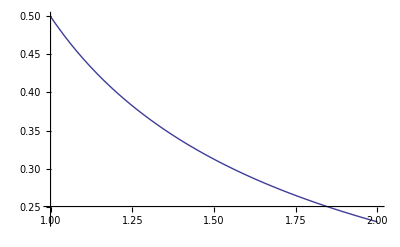

```mathematica
resu==0/.{Ma->1,γ0->7/5}//Simplify
u[r]/.NDSolve[{%,u[1]==1/2},u,{r,1,2}]//First
Plot[%,{r,1,2},PlotRange->Full]
```

u[r]^2 (u[r]+6 r u'[r])==6 (u[r]+r u'[r])

InterpolatingFunction[{{1.,2.}},<>][r]

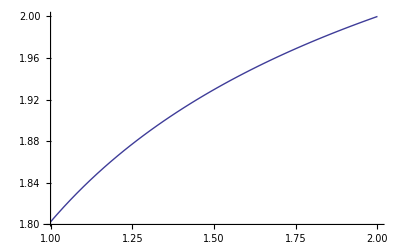

```mathematica
resu==0/.{Ma->1,γ0->7/5}//Simplify
u[r]/.NDSolve[{%,u[2]==2},u,{r,1,2}]//First
Plot[%,{r,1,2},PlotRange->Full]
```